## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T

```mathematica
(*The potential is V(x). Its support is [a,b]. We assume that m=hbar=1. c defines the interval for solving the Scoedinger equation*)
```

```mathematica
V[x_]:=1/Cosh[x]^2;
a=-10;
b=10;
c=4;
```

```mathematica
(*Here we solve the Schroedinger equation assuming that to the right of the potential (x>b) we have the outgoing wave of unit flux*)
```

```mathematica
SchrEq[k0_]:=Module[{k=k0},
NDSolve[{-f''[x]/2+V[x]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}];
];
```

```mathematica
(*Here we find the wave function to the left of the potential (x<a). This is done by fitting the solution of the Schroedinger equation using the Exp[\pm ISqrt[2] k x] basis. step determines the number of points used for fitting. Note that we can find the wave function also by numerical differentiation.*)
```

```mathematica
step=1;
WaveFuncLeft[k0_]:=Module[{help=SchrEq[k0]},Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k0,a,step/k0}],{Exp[I Sqrt[2]k0 x],Exp[-I Sqrt[2]k0 x]},x]];
```

```mathematica
(*Here we find the transmission coefficient -- it is determined by the coefficient in front of the incoming wave*)
```

```mathematica
T[k_]:=1/(WaveFuncLeft[k][[2]]/.x->0);
```

```mathematica
(*Now we check the solution using the exact result*)
```

```mathematica
t=Table[{k,Abs[T[k]]^2},{k,0.001,2,0.05}];
lp=ListPlot[t,PlotRange->All];
```

ReplaceAll::reps: {Null} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

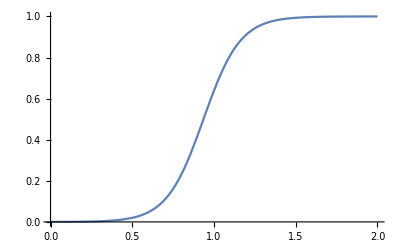

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

## Packaging the above routines as a function of the potential

```mathematica
SEDict=Association["a"->-10, "b"->10, "c"->4];
```

```mathematica
SchrEqOfV[V_,VParams_,SEDict_,k_]:=Module[{a,b,c, sol},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];

sol = NDSolve[{-f''[x]/2+V[x, VParams]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}];
Return[sol];
];
```

```mathematica
VTest[x_,params_]:=Module[{a,b,c,pot},
(* Extract params*)
a=params[[1]];
b=params[[2]];
c=params[[3]];
(* Calculate potential *) 
pot = a/Cosh[(x-b)/c]^2;
Return[pot]
];
```

```mathematica
VParamsTest = {1,0,1};
```

```mathematica
func=(f/.SchrEqOfV[VTest, VParamsTest, SEDict,1][[1]])
```

InterpolatingFunction[{{-14., 10.}}, <>]

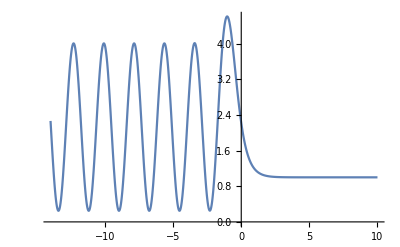

```mathematica
Plot[Abs[func[x]]^2,{x,-14,10}]
```

```mathematica
WaveFuncLeftOfV[V_, VParams_, SEDict_, k_,step_:1]:=Module[{a,b,c,help=SchrEqOfV[V,VParams,SEDict,k]},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];
Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k,a,step/k}],{Exp[I Sqrt[2]k x],Exp[-I Sqrt[2]k x]},x]
];
```

```mathematica
TofV[V_,VParams_, SEDict_,k_,step_:1]:=1/(WaveFuncLeftOfV[V, VParams,SEDict,k,step][[2]]/.x->0);
```

```mathematica
t=Table[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.01}];
lp=ListPlot[t,PlotRange->All];
```

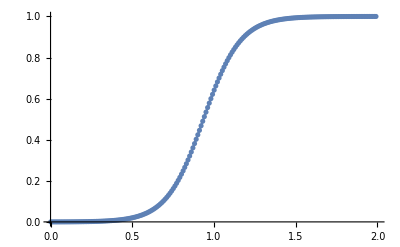

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

## Timing

```mathematica
res = ParallelTable[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.001}]//Timing;
```

```mathematica
res[[1]] (*seconds*)
```

0.113308

```mathematica
Length[res[[2]]]
```

2000

```mathematica
(*SE solutions per second*)
```

```mathematica
Length[res[[2]]]/res[[1]]
```

17651.

## TofKVec

```mathematica
getKVec[kmin_,kmax_,knum_]:=Table[k,{k,kmin,kmax,(kmax-kmin)/(knum-1)}]
```

```mathematica
TofVVec[V_,VParams_,SEDict_,kVec_]:=ParallelTable[{k,TofV[VTest, VParams, SEDict, k]},{k,kVec}]
```

```mathematica
kVecTest=getKVec[0.01,2,100];
```

## Cost

```mathematica
Cost[T_, TGoal_]:=
Module[{Tdiff, cost},
(*Calculate difference in vectors*)
Tdiff=Table[{T[[i,1]],Abs[T[[i,2]]-TGoal[[i,2]]]^2},{i,1,Length[T]}];

(*Calculate loss. Estimate integral using midpoint rule. Normalize by interval. *)
cost = Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (Tdiff[[i,2]]+Tdiff[[i+1,2]]),{i,1,Length[T]-1}] / (T[[Length[T],1]]-T[[1,1]]);
Return[cost];
];
```

```mathematica
TGoalTest=Table[{x,Sqrt[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2)]},{x,kVecTest}];
```

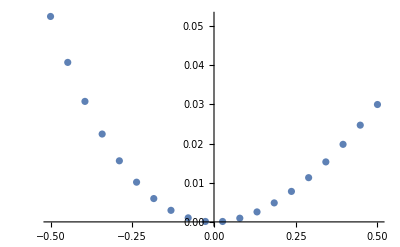

```mathematica
(* Plot the cost as a function of "a=1+eps", the coefficient of the Sech^2 potential. "eps=0" should reproduce the analytic results. *)
(* Getting lots of errors here, but the plot works fine. May have to worry more about these in the NMinimize routine. *)
ListPlot[Table[{eps,Cost[Abs[TofVVec[VTest,{1+eps,0,1},SEDict,kVecTest]],TGoalTest]},{eps,-0.5,0.5,1/19}]]
```

## Differential Evolution

```mathematica
(* Minimize the parameters of the potential to find the known solution. *)
```

```mathematica
(*NMinimize[{Hold[Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]],{v3>0}},{v1,v3}, 
Method->{"DifferentialEvolution", "Tolerance"->0.02}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:>Hold[Print["Params: ",{v1,0,v3} , " Cost: ", Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]]]]*)
```

## Gaussian Potential

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_,n_]:=Module[{pot},
pars=Table[{params[[i]],params[[i+1]],params[[i+2]]},{i,1,3*n,3}];

pot=Sum[VGauss[x,pars[[i]]],{i,1,n}];
Print[pot];
Return[pot];
];
```

```mathematica
n=5;
parsTest=RandomReal[{-3,3},n*5];
VGaussN[x,parsTest,n]
```

2.84458 ⅇ^(-0.223819 (-2.8867+x)^2)+1.9471 ⅇ^(0.169037 (-2.81502+x)^2)-2.81561 ⅇ^(-0.181149 (-2.04778+x)^2)+2.71078 ⅇ^(0.63177 (0.56815+x)^2)+2.19055 ⅇ^(-0.211237 (1.3207+x)^2)

```mathematica
NMinimize[{
Hold[Cost[Abs[TofVVec[VGaussN[x,{A1,x01,sigma1,A2,x02,sigma2},2],SEDict,kVecTest]], TGoalTest]],
{sigma1>0.01,sigma2>0.01,x01+x02==0}
},
{A1,x01,sigma1,A2,x02,sigma2}, 
Method->{"DifferentialEvolution", "Tolerance"->0.001}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:> Hold[Print["Params: ",{A1,x01,sigma1,A2,x02,sigma2} , " Cost: ", Cost[Abs[TofVVec[VTest,{A1,x01,sigma1,A2,x02,sigma2},SEDict,kVecTest]], TGoalTest]]]]
```

0.917412 ⅇ^(-0.411524 (-0.332112+x)^2)+0.212654 ⅇ^(-0.256277 (0.332112+x)^2)

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

A2 ⅇ^(-(x-x02)^2/(2 sigma2))+A1 ⅇ^(-(x+1. x02)^2/(2 sigma1))

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

NMinimize::nnum: The function value Indeterminate is not a number at {A1,A2,sigma1,sigma2,x01,x02} = {0.917412,0.212654,1.215,1.95101,0.332112,-0.332112}.

0.917412 ⅇ^(-0.411524 (-0.332112+x)^2)+0.212654 ⅇ^(-0.256277 (0.332112+x)^2)

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

A2 ⅇ^(-(x-x02)^2/(2 sigma2))+A1 ⅇ^(-(x+1. x02)^2/(2 sigma1))

NMinimize::nnum: The function value Indeterminate is not a number at {A1,A2,sigma1,sigma2,x01,x02} = {0.917412,0.212654,1.215,1.95101,0.332112,-0.332112}.

0.917412 ⅇ^(-0.411524 (-0.332112+x)^2)+0.212654 ⅇ^(-0.256277 (0.332112+x)^2)

A2 ⅇ^(-(x-x02)^2/(2 sigma2))+A1 ⅇ^(-(x+1. x02)^2/(2 sigma1))

NMinimize::nnum: The function value Indeterminate is not a number at {A1,A2,sigma1,sigma2,x01,x02} = {0.917412,0.212654,1.215,1.95101,0.332112,-0.332112}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

0.917412 ⅇ^(-0.411524 (-0.332112+x)^2)+0.212654 ⅇ^(-0.256277 (0.332112+x)^2)

A2 ⅇ^(-(x-x02)^2/(2 sigma2))+A1 ⅇ^(-(x+1. x02)^2/(2 sigma1))

NMinimize[{Hold[Cost[Abs[TofVVec[VGaussN[x,{A1,x01,sigma1,A2,x02,sigma2},2],SEDict,kVecTest]],TGoalTest]],{sigma1>0.01,sigma2>0.01,x01+x02==0}},{A1,x01,sigma1,A2,x02,sigma2},Method→{DifferentialEvolution,Tolerance→0.001},AccuracyGoal→2,PrecisionGoal→2,StepMonitor:>Hold[Print[Params: ,{A1,x01,sigma1,A2,x02,sigma2}, Cost: ,Cost[Abs[TofVVec[VTest,{A1,x01,sigma1,A2,x02,sigma2},SEDict,kVecTest]],TGoalTest]]]]